Two atom basis lattice vibrations (phonon modes)

```mathematica
ClearAll[numFrequenciesPerQ, rcap, scap, vR, vS, rn, maxQ, alphaF, betaF, mA, mB, mM] ;

(* 4 angular frequencies for 2 atom basis *) 
numFrequenciesPerQ = 4 ;

rcap::usage = "rcap(theta)" ;
rcap = {Cos[#], Sin[#]} & ;
scap = {-Cos[#], Sin[#]} & ;

vR::usage = "vR(a, theta).  The North-east pointing primitive cell vector for the diamond lattice.  a is the length of this vector, and 2 theta is the angular separation of the pair of primitive cell vectors." ;
vR = #1 rcap[#2] & ;
vS = #1 scap[#2] &;

rn::usage = "rn({n1, n2}, a, theta).  This is the position of the origin of the {n1, n2} unit cell." ;
rn = #1[[1]] vR[#2, #3] + #1[[2]] vS[#2, #3]  &;

maxQ::usage = "maxQ(a, theta).  This is the maximum length for either of the reciprocal frame vectors for this diamond lattice.

Note that the reciprocal vectors are g = (Pi/a)(pm/Cos[theta], Sin[theta]), with norm: 2 Pi/(a Sin[2 theta]))" ;
maxQ = 2 Pi/(#1 Sin[2 #2]) & ;

alphaF::usage = "alphaF( a, theta, k3, pm k4, {qx, qy})" ;
alphaF = #3 Sin[vR[#1, #2] . #5/2]^2 + #4 Sin[vS[#1, #2]  . #5/2]^2 &;

betaF::usage = "betaF( a, theta, k1, pm k2, {qx, qy})" ;
betaF = #3 Cos[(vR[#1, #2] - vS[#1, #2] ) . #5/2] + #4 Cos[(vR[#1, #2] + vS[#1, #2] ) . #5/2]& ;

mA::usage = "mA(k1, k2, theta, alphaPlus, alphaMinus)" ;
mA = {{#1 + #4(1 + Cos[2 #3]), #5Sin[2 #3]} , {#5Sin[2 #3], #2 + #4(1 + Cos[2 #3])}} & ;

mB::usage = " mB(a, theta, qy, betaPlus, betaMinus) " ;
mB = E^(I #1 Sin[#2] #3){ 
{#4(1 + Cos[2 #2]), #5Sin[2 #2]} , {#5Sin[2 #2], #4(1 + Cos[2 #2])}} & ;

mM::usage = "This is the final matrix equation to solve for ω^2, and the corresponding eigenvectors {e1, e2}.

mM(#1,         #2,#3,#4,#5,#6,#7   ,#8       ,#9        ,#10     ,#11      ,#12)
mM(omegaSquare,k1,k2,m1,m2,a ,theta,alphaPlus,alphaMinus,betaPlus,betaMinus,qy)

See: https://sites.google.com/site/peeterjoot3/math2014/twoMassHarmonic.pdf to understand how this matrix equation was arrived at (and an explaination of the helper submatrix variables above).
" ;
mM=ArrayFlatten[{{#1 IdentityMatrix[2]-2 mA[#2,#3,#7,#8,#9]/#4,mB[#6,#7,-#12,#10,#11]/Sqrt[#4 #5]},{mB[#6,#7,#12,#10,#11]/Sqrt[#4 #5],#1 IdentityMatrix[2]-2 mA[#2,#3,#7,#8,#9]/#5}}]&;

(*
ClearAll[d] ;
d = Collect[ Det[ mM[## ] ], {#1, #4, #5}, Simplify] &;

(* display equation to solve for ω^2 *)
mM[ω^2,Subscript[k, 1],Subscript[k, 2],Subscript[m, 1],Subscript[m, 2],a,θ,α_+,α_-,β_+,β_-,Subscript[q, y]] // TraditionalForm // MatrixForm

(* A full expansion of the Determinant for above, Simplified term by term in powers of ω^2 *)
d[ω^2,Subscript[k, 1],Subscript[k, 2],Subscript[m, 1],Subscript[m, 2],a,θ,α_+,α_-,β_+,β_-,Subscript[q, y]] // TraditionalForm*) 
 
ClearAll[qTable] ;
qTable::usage = "Do the computation of the matrix to solve for each q in the range of interest, and pass back the data." ;
qTable[{k1_, k2_, k3_, k4_, m1_, m2_, a_, theta_, qiSys_, qiEig_}] := Module[{mE, alpha, beta, vv, qMax, eigenSystemTable, eigenValueTable,e, t, len},
 
qMax = maxQ[a, theta] ;

alpha[qq_, sign_] := alphaF[a, theta, k3, sign k4, qq] ;
beta[qq_, sign_] := betaF[a, theta, k1, sign k2, qq] ;

(*ω^2,Subscript[k, 1],Subscript[k, 2],Subscript[m, 1],Subscript[m, 2],a,θ,α_+,α_-,β_+,β_-,Subscript[q, y]*)
mE[qq_List] := -mM[0,k1, k2, m1, m2, a, theta, alpha[qq, 1], alpha[qq, -1], beta[qq, 1], beta[qq, -1], qq[[2]]] ;

eigenSystemTable = Flatten[ Table[ {qx, qy, mE[{qx, -qy}] // N},{qx, -qMax/2, qMax/2, qMax/qiSys}, {qy, -qMax/2, qMax/2, qMax/qiSys}], 1] ;
 
e = Eigensystem[ #[[3]] ] &/@ eigenSystemTable ;
(*e*)
len = Length[e] ;

t= Table[
Sort[{Sqrt[#[[1]]], Take[#[[2]], 2], Drop[#[[2]], 2]} &/@ (e[[i]] // Transpose), #1[[1]] < #2[[1]] &], {i, len}] ;
(*t*)

eigenValueTable =Flatten[Table[{{qx, qy}, Eigenvalues[mE[{qx, -qy}]]},{qx, -qMax/2, qMax/2, qMax/qiEig}, {qy, -qMax/2, qMax/2, qMax/qiEig} ], 1] ;

(*Take[eigenValueTable, 3]*)
(*eigenValueTable // N*)

{Table[{Take[eigenSystemTable[[i]], 2], t[[i]]}, {i, len}], eigenValueTable}
] ;

ClearAll[tableOfEpsilonsByQandOmegaForOneQPoint] ;
tableOfEpsilonsByQandOmegaForOneQPoint::usage = "Consume intermediate results of qTable[] and rescale the e1,e2 eigenvector components by the masses." ;
tableOfEpsilonsByQandOmegaForOneQPoint[{m1_, m2_}, j_, i_, results_]:= Module[{q, omega, e1, e2},

q = results[[j]][[1]] ;
{omega, e1, e2} = results[[j]][[2]][[i]] ;

{
q, 
omega,
e1/Sqrt[ m1 ],
e2/Sqrt[ m2]

}
] ;

ClearAll[ precomputationOfStuffIndependentOfQandOmegaAndTime ] ;
precomputationOfStuffIndependentOfQandOmegaAndTime::usage = "precomputationOfStuffIndependentOfQandOmegaAndTime({k1, k2, k3, k4, m1, m2, a, theta, qi, qi2})" ;
precomputationOfStuffIndependentOfQandOmegaAndTime[{k1_, k2_, k3_, k4_, m1_, m2_, a_, theta_, qi_, qi2_}]:= Module[{r, e, f, l, g, yoffsets, qf,pointsRange, pointsN},

{r,e} = qTable[{k1, k2, k3, k4, m1, m2, a, theta, qi, qi2}]  ;

f = Flatten[Table[
tableOfEpsilonsByQandOmegaForOneQPoint[ {m1, m2}, j, i, r]
, {j, Length[r]}
,{i, numFrequenciesPerQ} 
],1] ;

l = Flatten[ {
Table[ { 
rn[{i, -3}, a, theta ],
rn[{i, 3},a, theta ]
} ,{i, -3, 3}],
Table[ { 
rn[{-3, i},a, theta ],
rn[{3, i},a, theta ]
} ,{i, -3, 3}]}, 1] ;

yoffsets = {1/2, 3/2} ;
(* f({i,j}_List, t, [12], omega, q_List, e_List) *)
g= rn[#1,a, theta ] + {0, yoffsets[[#3]] a Sin[ theta ]}  + Re[ #6[[#3]] Exp[ I(rn[#1, a, theta ] . #5 - #4 #2) ] ]& ;

(* f( qManip ) *)
qf = Pi Round[# qi /2]/(qi/2)/( a Sin[2 theta] ) & ;


{f, l, g, qf,PointSize[Sqrt[m1]/200], PointSize[Sqrt[m2]/200], e}
] ;

(* Based on a ListLinePlot version posted in: http://mathematica.stackexchange.com/a/37228/10 *)
ClearAll[springPoints]
springPoints::usage = "springPoints[ point1, point2, numberOfTurns, height, fractionToDrawAsLinesAtEnds ].  Example:

ListLinePlot[springPoints[{1,2},{3,5}], AspectRatio→Automatic ]" ;
springPoints[ a1_List, a2_List, n_Integer:8,h_:.05, f_: 0.1 ] :=Module[{n1, d, nd, r, r1 },

n1 = Norm[a1] ;
d = a2 - a1 ;
nd = Norm[d] ;
r = RotationMatrix[ArcTan @@  d ] ;
r1 = r . {n1, 0} ;

{
Table[ a1 -r1 + r . { n1 + nd f + t (1 - 2f) nd, h Sin[ 2 Pi n t]}, {t, 0, 1, 0.01 } ],
Table[ a1 -r1 + r . { n1 + nd f + (1 - 2f) nd + t f nd, 0}, {t, 0, 1, 0.01 } ],
Table[ a1 -r1 + r . { n1 +t f nd, 0}, {t, 0, 1, 0.01 } ]
}
]
```

```mathematica
Manipulate[
DynamicModule[{  (*qi,*) resultsTable, lines, g, qf, sz1, sz2,p,pointsRange, eigenValuesTable  },

(*qi = 4 ;*)

{resultsTable, lines, g, qf, sz1, sz2, eigenValuesTable} = precomputationOfStuffIndependentOfQandOmegaAndTime[ {k1, k2, k3, k4, m1, m2, a, theta, 4 (* qi*), 16 (* qi2 *) } ] ;

pointsRange = 2 ;
(* pointsN(t, [12], omega, q, e) *)
p := Flatten[ Table[ g[{i, j}, ##], {i, -pointsRange-1, pointsRange}, {j, -pointsRange-1, pointsRange}], 1 ] & ;

Dynamic@Module[{q,select, omega, e,   points1, points2},
q = qf[ qManip ] ;

select = Select[ resultsTable, #[[1]] == q & ][[n]] ;
omega = select[[2]] ;
e = Take[ select, -2] ;

(* functions of time. *)
points1 = p[ #, 1, omega, q, e ] & ;
points2 = p[ #, 2, omega, q, e ] & ;

Grid[{
{Module[{mList1, mList2, prange, bothLists, springData, springCoords,coordList, mSelect},

springCoords=
{{Orange,{{-1,0},2},{{0,0},1} (*k1*)},
{Orange,{{0,-1},2},{{0,0},1} (*k1*)},
{Green,{{0,0},1},{{0,0},2} (*k2*)},
{Green,{{0,0},1},{{-1,-1},2} (*k2*)},
{Purple,{{1,0},1},{{0,0},1} (*k3*)},
{Purple,{{-1,0},1},{{0,0},1} (*k3*)},
{Cyan,{{0,1},1},{{0,0},1} (*k4*)},
{Cyan,{{0,-1},1},{{0,0},1} (*k4*)}};

springData = {#[[1]], 
springPoints[g[#[[2]][[1]], 0, #[[2]][[2]],omega, q, e],
g[#[[3]][[1]], 0, #[[3]][[2]],omega, q, e]]
} &/@ springCoords  ;

coordList = Flatten[springCoords[[All, {2,3}]], 1] // DeleteDuplicates;

mSelect[i_] := Select[ coordList, #[[2]] == i & ] ;

{mList1, mList2} = Table[g[#[[1]], 0, #[[2]],omega, q, e] &/@ mSelect[j],{j, 2}] ;

bothLists = Flatten[ {mList1, mList2}, 1] // Transpose ;
prange = { Min[ bothLists[[#]] ], Max[ bothLists[[#]] ] } * 1.1 &;

Show[{
ListLinePlot[ #, 
PlotRange -> (prange[#] &/@ Range[2])
, AspectRatio->Automatic
, PlotLabel->"Interaction legend"
, PlotStyle->LightGray
] &/@ lines,
ListPlot[ mList1,
PlotStyle->{sz1, Red}
],
ListPlot[ mList2,
PlotStyle->{sz2, Blue}
],
ListLinePlot[ #[[2]], 
 PlotStyle->Darker[#[[1]]]
] &/@ springData
}]
] (* Module *)
,
ListLinePlot[lines
, PlotRange -> {{-2, 2}, {-2, 2}}
, PlotLabel -> Row[{ "Lattice mass positions for ", Subscript[ω, n], "( ", q[[1]], " , ", q[[2]], " )"}]
, Epilog -> {sz1,Red, Point[points1[2 Pi tau/omega]], Blue, sz2,Point[points2[2 Pi tau/omega]]}
, AspectRatio->Automatic
]
,
Module[{t, oMin,oMax},
t[nn_] := Flatten[{#[[1]],Sqrt[#[[2]]][[nn]]}]&/@ eigenValuesTable  ;
oMin = eigenValuesTable[[All,2]] [[All,4]] // Min // Sqrt;
oMax = eigenValuesTable[[All,2]] [[All,1]] // Max // Sqrt;

Show[
ListPlot3D[  t[#] &/@ Range[4], PlotLabel -> Row[{Subscript[ω, "n"] ,"( ", OverVector["q"]," )"} ]],
Graphics3D[ {
Thick,
Line[{
Flatten[{q,oMin}],
Flatten[{q,oMax}]
} ](*,
PointSize -> Large, Point[Flatten[{q,omega}]]*)
} ] 
]
]
}
}
,ItemSize->Automatic
,ItemStyle->ImageSizeMultipliers->1
 ] (* Grid *)
] (* Dynamic@Module *)
] (* Manipulate *)
,{{k1, 0.5, Style["k_1", FontColor->Darker[Orange]]}, 0.25, 0.9,Appearance->"Labeled"}
,{{k2, 0.5, Style["k_2", FontColor->Darker[Green]]}, 0.25, 0.9,Appearance->"Labeled"}
,{{k3, 0.25, Style["k_3", FontColor->Darker[Cyan]]}, 0.25, 0.9,Appearance->"Labeled"}
,{{k4, 0.25, Style["k_4", FontColor->Darker[Purple]]}, 0.25, 0.9,Appearance->"Labeled"}
,{{m1, 10, Style["m_1", FontColor->Red]}, 5, 30,Appearance->"Labeled"}
,{{m2, 20, Style["m_2", FontColor->Blue]}, 5, 30,Appearance->"Labeled"}
,{{a, 1, "a"}, 0.5, 2,Appearance->"Labeled"}
,{{theta, Pi/3, "θ"},2.5Pi/8, 4 Pi/8,Appearance->"Labeled"}
(*,{{qi, 8, "q mesh size"}, 2, 20}*)
,{{n, 1, "ω_n: n = "}, 1, numFrequenciesPerQ, 1, Appearance->"Labeled", ContinuousAction->True}
, {{qManip,{0,0},OverVector["q"]},{-1, -1}, {1, 1},ContinuousAction->True }
, {{tau, 0, "t/T"}, 0, 1, ContinuousAction->True}
, SaveDefinitions->True
,ContinuousAction->None
]
```

A lattice of atoms can be modelled as harmonic oscillators, with forces proportional to the displacements of the atoms from equilibrium positions.  The simplest such model introduces coupling for only the nearest neighbour atoms.  In this demonstration, a lattice containing pairs of atoms, each with separate masses is modelled, with nearest neighbour harmonic coupling for each mass.  Normal mode solutions to these equations of motion are plotted.  Controls are provided to alter the coupling "spring constants" and other free parameters, as well as controls to select from the reciprocal space vectors, and angular frequencies associated with the normal mode solutions.  A time control is also provided to display changes of the lattice through one period of the lattice vibration.

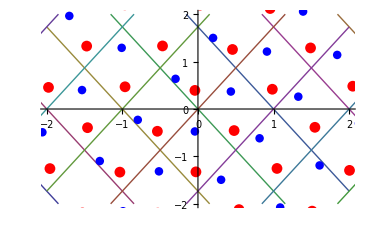

Trial solutions of the form: (u⃗)_(n,i)(r_n', t)= (OverVector[ϵ_i](q⃗))/(√m_i)e^(I (OverVector[r_(n⃗)]. q⃗ - ω t)) are used to find solutions for the system.

Here (u⃗)_(n,i)is a vector displacement for the mass in unit cell n, for mass i ; (r⃗)_(n⃗ = (n_1, n_2)) = n_1 s⃗ + n_2 t⃗ is the position of the n⃗'th unit cell, and s⃗,t⃗ are the unit cell vectors ; q⃗ is a vector in reciprocal space.  The vectors OverVector[ϵ_i](q) together form an eigenvector of the equations of motion of the system for this assumed solution, where ω^2 are the eigenvalues of this system.  For this two atom basis, there are four such ω^2 eigenvalues per q⃗ point, each with a different characteristic motion.  A control is available to pick between these characteristic angular frequencies.

Free parameters availble as controls in this demonstration include the spring constants k_i, the masses m_i, the primative unit cell lattice vectors (±a cos(θ), sin(θ)).

Change to any of these free parameters requires an update selection (U in the upper right corner) to make them take effect.

Three continuously updated controls are available, ω, q⃗, and t.  These can be varied for each selection of the set of free parameters, after update.

Selecting run for the time control will animate the lattice vibrations.

General theory describing oscillations around the lattice equilbrium points can be found in:

Neil W Ashcroft and N David Mermin. Solid State Physics. Holt, Rinehart and Winston, New York, 1976.  Chapters 21, 22.

Resize Images

Rotate and Zoom in 3D

Drag Locators

Create and Delete Locators

Slider Zoom

Gamepad Controls

Automatic Animation

Bookmark Animation

two atom basis, lattice vibration, phonon, reciprocal lattice vector, angular frequency

Analysis of Lattice Vibrations in Two Dimensions

Motion of Atoms in Crystal

Simple Harmonic Motion for a Spring

Normal Modes in a Periodic Square Lattice

Contributed by: Peeter Joot